# ArnoudBuzing/EllipticIntegrals

Wolfram Language bindings for the Rust elliptic integrals crate

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"CarlsonRC.nb"DocumentationEnglishReferencePagesSymbolsCarlsonRC.nb

"CarlsonRD.nb"DocumentationEnglishReferencePagesSymbolsCarlsonRD.nb

"CarlsonRF.nb"DocumentationEnglishReferencePagesSymbolsCarlsonRF.nb

"CarlsonRG.nb"DocumentationEnglishReferencePagesSymbolsCarlsonRG.nb

"CarlsonRJ.nb"DocumentationEnglishReferencePagesSymbolsCarlsonRJ.nb

"Cel1.nb"DocumentationEnglishReferencePagesSymbolsCel1.nb

"Cel2.nb"DocumentationEnglishReferencePagesSymbolsCel2.nb

"Cel.nb"DocumentationEnglishReferencePagesSymbolsCel.nb

"El1.nb"DocumentationEnglishReferencePagesSymbolsEl1.nb

"El2.nb"DocumentationEnglishReferencePagesSymbolsEl2.nb

"El3.nb"DocumentationEnglishReferencePagesSymbolsEl3.nb

"EllipticD.nb"DocumentationEnglishReferencePagesSymbolsEllipticD.nb

"EllipticE.nb"DocumentationEnglishReferencePagesSymbolsEllipticE.nb

"EllipticF.nb"DocumentationEnglishReferencePagesSymbolsEllipticF.nb

"EllipticK.nb"DocumentationEnglishReferencePagesSymbolsEllipticK.nb

"EllipticPiBulirsch.nb"DocumentationEnglishReferencePagesSymbolsEllipticPiBulirsch.nb

"EllipticPi.nb"DocumentationEnglishReferencePagesSymbolsEllipticPi.nb

"Tutorials"

"Kernel"

"EllipticIntegrals.wl"KernelEllipticIntegrals.wl

"LibraryResources"

"MacOSX-ARM64"

"libellip_link.dylib"LibraryResourcesMacOSX-ARM64libellip_link.dylib

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

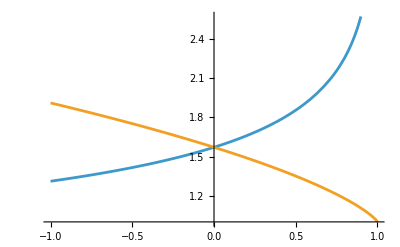

### Basic Description

The EllipticIntegrals paclet is a high-performance extension for the Wolfram Language that provides lightning-fast evaluation of classical Legendre elliptic integrals and Carlson symmetric forms. By leveraging a highly optimized Rust backend (ellip crate) compiled to native machine code and integrated via LibraryLink, the paclet bypasses the overhead of symbolic parsing and arbitrary-precision systems. This makes it an ideal tool for physical simulations, geodesic computations, and engineering pipelines that require evaluating elliptic functions over large numerical datasets at speed.

Benchmarks show substantial performance improvements—executing up to 7x faster than the built-in, general-purpose Wolfram Language implementations when evaluating machine-precision reals. By utilizing efficient, iterative arithmetic-geometric mean (AGM) algorithms and avoiding numerical caching bottlenecks, the package enables rapid processing of millions of coordinates in fractions of a second.

To achieve this level of execution speed, the library is strictly optimized for real-valued arguments in double-precision machine float format. Consequently, it does not support complex number arguments or arbitrary-precision evaluation. For complex inputs or arbitrary-precision bounds, the native, built-in Wolfram Language functions should be used as fallback mechanisms.

### Details

Additional information about the paclet.

### Primary Context

ArnoudBuzing`EllipticIntegrals`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad["/Users/arnoudb/github/EllipticIntegrals/EllipticIntegrals"];
```

```mathematica
Needs["ArnoudBuzing`EllipticIntegrals`"->"ei`"];
```

### Basic Examples

```mathematica
Plot[{ei`EllipticK[x],ei`EllipticE[x]},{x,-1,1}]
```

-Graphics-

Show a few simple examples of common uses of the paclet:

```mathematica
MyFunction[a,b,c]
```

a^2/(b+c)

### Scope

Give more examples showing the range of features in the paclet:

```mathematica
MyPlot[MyFunction[a,3,4],{a,1,10}]
```

-Graphics-

Use screenshots to show features like notebook styles, palettes and external operations:

```mathematica
ViewWebsite["wolframcloud"]
```

-Graphics-

## Source & Additional Information

### Creator

Arnoud Buzing

### Source Control Repository

https://github.com/arnoudbuzing/EllipticIntegrals

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

14.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.